```mathematica
r=0.00002 ; (*tube radius*); d=2*r;  (*tube diameter*)
l=0.0001; (*tube length*)
k=6.626070*10^(-34); (*Boltzmann Constant*)
T=273.15+25; (*room temperature*)
rho=997; (*water density*)
NA=6.02214086×10^23 ; (*Avogadro Constant*)
my=0.00089; (*water dynamic viscosity*)
m=0.018015/NA ;(*mass of a single water molecule*)
pv=3168.5747474290; (*vapour pressure water at room temperature*)
va=Sqrt[(8*k*T)/(Pi*m)] ;(*average velocity of water molecule in gas*)
A=(8*my*m*pv*va)/(d*d*rho*k*T);

p0[h_]:=2pv+2A*(14l+4l/d*h-14h-4/d*h*h)/(14+18/d*h+3/d/d*h*h)

Solve[p==2pv+2A*(14l+4l/d*h-14h-4/d*h*h)/(14+18/d*h+3/d/d*h*h)&& 0<h<l,h,Reals] (*Find the inverse function h(p)*)
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{h→ConditionalExpression[-(2.97652×10^-18 (6.44869×10^23+4.30521×10^18 p))/(9.9357×10^10+106788. p)+2.67275×10^-31 √((2.00645×10^75+1.68074×10^69 p+1.1068×10^63 p^2)/((9.9357×10^10+106788. p)^2)),6337.15<p<1.76274×10^6]}}

```mathematica
h[p_]:=(-(2.976521450372251*^-18 (6.448688918248039*^23+4.3052133887351567*^18 p))/(9.9356962061*^10+106788. p)+2.6727504668333677*^-31 √((2.0064548328946743*^75+1.6807374641226172*^69 p+1.1068025670117018*^63 p^2)/((9.9356962061*^10+106788. p)^2)))

z[p_]:=l-h[p] (*z-coordinate of the liquidlevel inside the tube*)
```

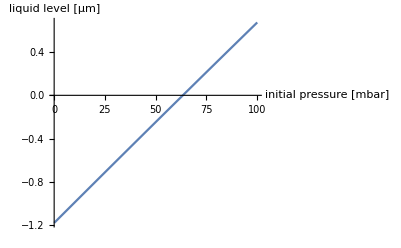

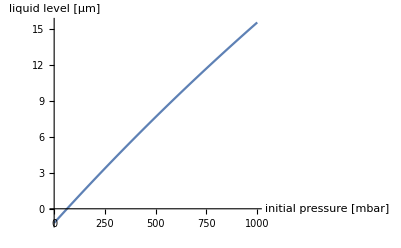

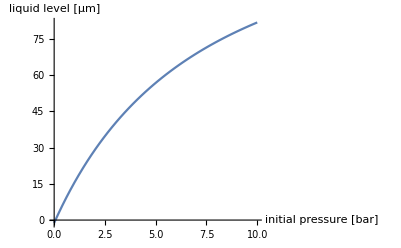

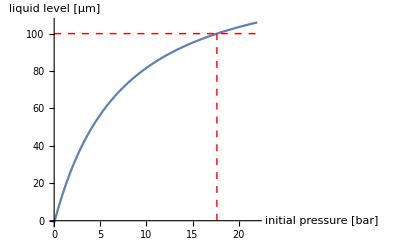

```mathematica
Plot[{(z[100p]*10^6)},{p,0,100},AxesLabel->{"initial pressure [mbar]","liquid level [μm]"}]
Plot[{(z[100p]*10^6)},{p,0,1000},AxesLabel->{"initial pressure [mbar]","liquid level [μm]"}]
Plot[{(z[100000p]*10^6)},{p,0,10},AxesLabel->{"initial pressure [bar]","liquid level [μm]"}]
line1=Line[{{17.627440066778434,0},{17.627440066778434,l*10^6}}];
Plot[{(z[100000p]*10^6),l*10^6},{p,0,22},PlotStyle->{Automatic,Directive[lineStyle]},Epilog->{Directive[lineStyle],line1},AxesLabel->{"initial pressure [bar]","liquid level [μm]"}]
```